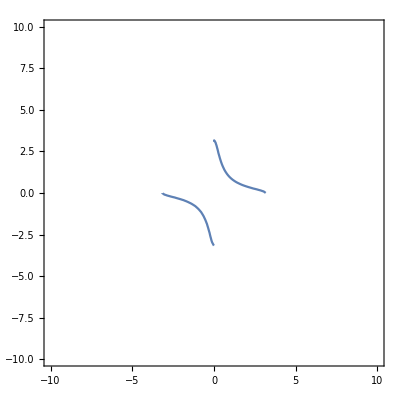

```mathematica
ContourPlot[x y - √(1-0.1 x^2)√(1-0.1 y^2)==1/100,{x,-10,10},{y,-10,10}]
```

```mathematica
Plot3D[x y - √(1-0.01 x^2)√(1-0.01 y^2),{x,-10,10},{y,-10,10},AspectRatio->1]
```

-Graphics3D-

```mathematica
r = {x,y,z};
p = {px,py,pz};
```

```mathematica
r.r
```

x^2+y^2+z^2

```mathematica
(3p.r r - p (r.r))/(r.r)^(5/2)
```

```mathematica
{(3 x (px x+py y+pz z)-px (x^2+y^2+z^2))/((x^2+y^2+z^2)^(5/2)),(3 y (px x+py y+pz z)-py (x^2+y^2+z^2))/((x^2+y^2+z^2)^(5/2)),(3 z (px x+py y+pz z)-pz (x^2+y^2+z^2))/((x^2+y^2+z^2)^(5/2))}//Expand
```

{(2 px x^2)/((x^2+y^2+z^2)^(5/2))+(3 py x y)/((x^2+y^2+z^2)^(5/2))-(px y^2)/((x^2+y^2+z^2)^(5/2))+(3 pz x z)/((x^2+y^2+z^2)^(5/2))-(px z^2)/((x^2+y^2+z^2)^(5/2)),-(py x^2)/((x^2+y^2+z^2)^(5/2))+(3 px x y)/((x^2+y^2+z^2)^(5/2))+(2 py y^2)/((x^2+y^2+z^2)^(5/2))+(3 pz y z)/((x^2+y^2+z^2)^(5/2))-(py z^2)/((x^2+y^2+z^2)^(5/2)),-(pz x^2)/((x^2+y^2+z^2)^(5/2))-(pz y^2)/((x^2+y^2+z^2)^(5/2))+(3 px x z)/((x^2+y^2+z^2)^(5/2))+(3 py y z)/((x^2+y^2+z^2)^(5/2))+(2 pz z^2)/((x^2+y^2+z^2)^(5/2))}

```mathematica
{px,py,pz}.{x,y,z}
```

px x+py y+pz z

```mathematica
3/2 a ((1-√(1-3 a^2/c1^2))/(3a)+u1)^2+a/(2 c1^2)-((1-√(1-3 a^2/c1^2))/(3a)+u1)//Expand
```

-√(1-(3 a^2)/c1^2) u1+(3 a u1^2)/2

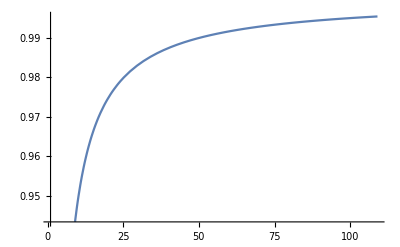

```mathematica
Plot[√(1-1/x),{x,1,109}]
```